## Generating Data

```mathematica
(* centers data where batch dimension is 1 *)
centerData[X_]:=Module[{Xc},
Xc=Mean@Transpose@X;
Transpose[#-Xc&/@Transpose[X]]
];

generateXY[e_,yvar_,dsize_]:=Module[{wt,mean,cov,normal,pdf,X,Xc,Y,Xa,wta,w0a,XY,n,trueCov},
SeedRandom[0];
n=2;
wt={{1,1}}; (* true relation *)
mean=0&/@Range@n;
cov={{1, 1-e},{1-e,1}};
normal=MultinormalDistribution[mean,cov];
X=RandomVariate[normal,{dsize}]//Transpose;
X=centerData[X];
Y=Dot[wt, X]+RandomVariate[NormalDistribution[0,√yvar]];
{X,Y,wt}
];
```

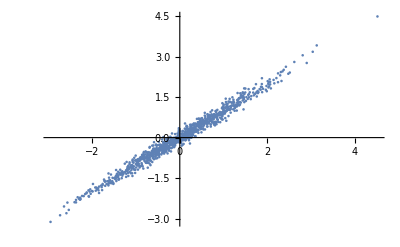

```mathematica
{X,Y,w0}=generateXY[0.01,1.,1000];
ListPlot[Transpose@X]
```

```mathematica
X//Dimensions
```

{2,1000}

```mathematica
H=X.Transpose[X]
```

{{1034.75,1025.11},{1025.11,1036.19}}

```mathematica
n=5;
G=Table[RandomReal[{-1,1},{2,2}],{n}]
```

{{{0.596533,0.454156},{0.451236,0.561135}},{{-0.665353,-0.577862},{0.441155,-0.920482}},{{-0.599461,0.165057},{0.270707,-0.230497}},{{-0.953261,-0.586907},{-0.520693,0.0334766}},{{0.044169,0.0684878},{-0.177357,-0.346207}}}

```mathematica
H=Total[vec[#].Transpose[vec[#]]&/@G]
```

{{2.06856,0.301898,1.11896,1.03815},{0.301898,0.774091,0.288139,-0.171297},{1.11896,0.288139,0.916577,0.705351},{1.03815,-0.171297,0.705351,1.33627}}

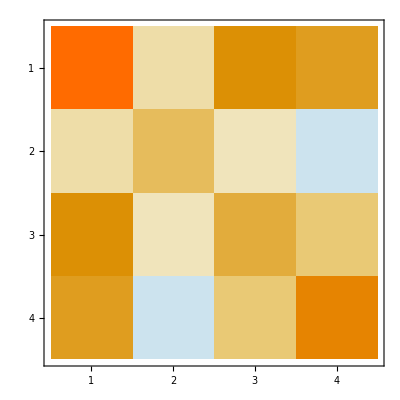

```mathematica
H//MatrixPlot
```

```mathematica
sqrt[m_]:=#[[1]].Sqrt@#[[2]].Transpose@#[[1]]&@SingularValueDecomposition@m
```

```mathematica
H2=sqrt[Total[#.Transpose[#]/2&/@G]]⊗sqrt[Total[Transpose[#].#/2&/@G]]
```

{{1.40747,0.257038,0.268291,0.0489964},{0.257038,1.2475,0.0489964,0.237797},{0.268291,0.0489964,1.17446,0.214485},{0.0489964,0.237797,0.214485,1.04097}}

```mathematica
H
```

{{2.06856,0.301898,1.11896,1.03815},{0.301898,0.774091,0.288139,-0.171297},{1.11896,0.288139,0.916577,0.705351},{1.03815,-0.171297,0.705351,1.33627}}

```mathematica
Eigenvalues[H2]
```

{1.79633,1.19062,1.1327,0.750759}

```mathematica
Eigenvalues[H]
```

{3.50978,1.03657,0.378918,0.17023}

```mathematica
H2=sqrt[Total[#.Transpose[#]/2&/@G]]⊗sqrt[Total[Transpose[#].#/2&/@G]]
```

## Rank approximations of symmetric matrix

## Newton Decrement

{x1,x2}

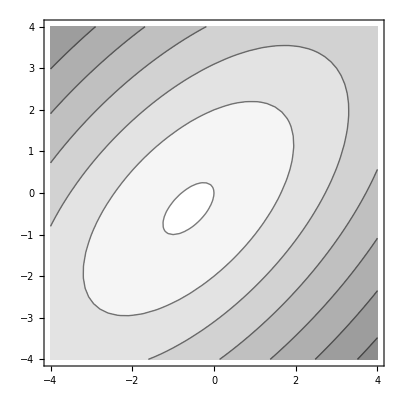

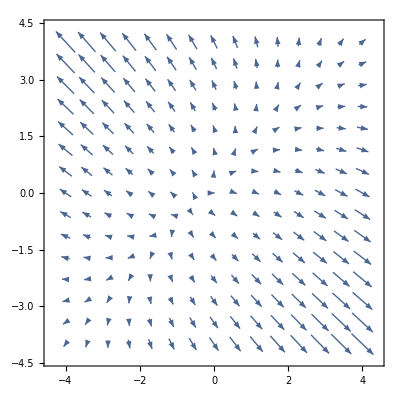

```mathematica
g=RotationMatrix[Pi/4];
A=g.{{1,0},{0,4}}.Inverse[g];
b=v2c@{1,0};
loss[x_]:=toscalar[1/2 xᵀ.A.x+bᵀ.x+4];
grad[x_]:=A.x+b;
xvar={x1,x2}
ContourPlot[Sqrt@loss[v2c@{x1,x2}],{x1,-4,4},{x2,-4,4},ColorFunction->Function[GrayLevel[1 - .45 #]]]
grads=D[loss[v2c@{x1,x2}],{{x1,x2},1}];
VectorPlot@@{grads,{x1,-4,4},{x2,-4,4}}
```

### Minimize

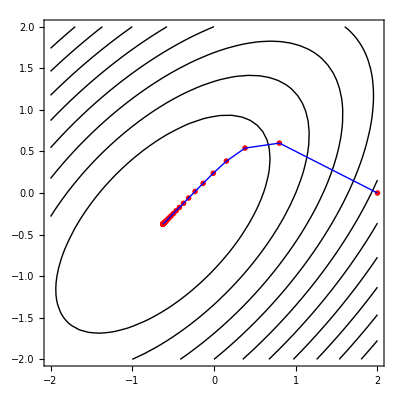

```mathematica
w0=v2c@{2,0};
pointList={};
gradList={};
lossList={};
iters=10;
w=w0;
lr=0.2;
iters=50;
For[iter=1,iter≤iters,iter++,pointList=pointList~Append~w;
gradList=gradList~Append~grad[w];
lossList=lossList~Append~loss[w];
w=w-lr*grad[w]
];

plt1=ContourPlot[Sqrt@loss[v2c@{x,y}],{x,-2,2},{y,-2,2},Contours->10,ContourShading->None];
plotPoints=Flatten/@pointList[[;;50]];
plt2=Graphics[{Red,PointSize[0.01],Point[plotPoints]}];
plt3=Graphics[{Blue,Line[plotPoints]}];
Show[plt1,plt2,plt3]
```

#### Plot in whitened coordinates

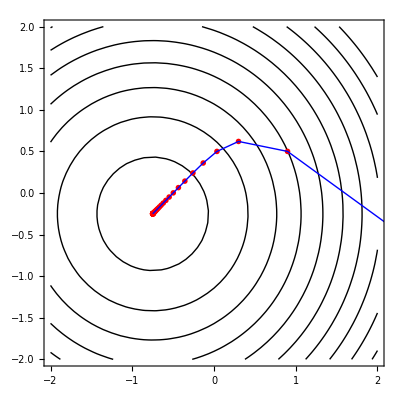

```mathematica
whiten=Inverse@symsqrt[A];
unwhiten=symsqrt[A];
plt1=ContourPlot[Sqrt@loss[whiten.v2c@{x,y}],{x,-2,2},{y,-2,2},Contours->10,ContourShading->None];
plotPoints2=unwhiten.#&/@(Flatten/@pointList[[;;50]]);
plt2=Graphics[{Red,PointSize[0.01],Point[plotPoints2]}];
plt3=Graphics[{Blue,Line[plotPoints2]}];
Show[plt1,plt2,plt3]
```

#### Take Newton step

```mathematica
loss[w0]
```

11

```mathematica
wopt=-Inverse[A].b;
loss[wopt]//N
```

3.6875

```mathematica
lambda=symsqrt[bᵀ.Inverse[A].b]//N
```

{{0.790569}}

```mathematica
lambda^2/2//N
```

{{0.3125}}

```mathematica
-1/2 lambda^2+4
```

{{3.6875}}